```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY189/morning_sec_int_data/778nm.dat"]
```

{{1.12389,-0.016658},{1.13423,-0.0117083},{1.14739,-0.013146},{1.16401,-0.00651115},{1.183,-0.0122345},{1.20042,-0.00781042},{1.22646,-0.0282349},{1.24828,-0.0259539},{1.27782,-0.0203864},{1.30453,-0.0168105},{1.34407,-0.00941417},{1.38078,-0.0296657},{1.41705,-0.0238215},{1.46132,-0.0276076},{1.51023,-0.0393959},{1.58758,-0.0316661},{1.63065,-0.0440146}}

0.0517456-0.0557126 x

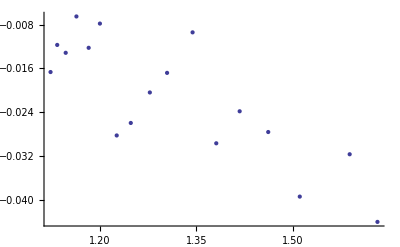

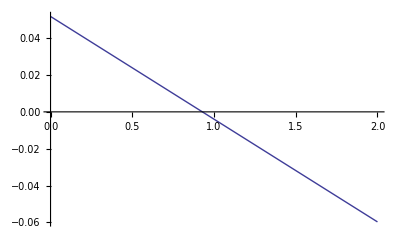

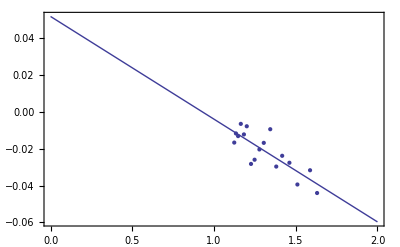

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```